```mathematica
me=9.1*10^-31;
qe=1.6*10^-19;
```

```mathematica
a=0.001*1/4*25.4
Icurrent=45;
μ0=N[4*π*10^-7];
B0=(μ0*Icurrent)/(2*a);
numloops=10;
totallength=a/10;
Vacc=20000;
```

0.00635

```mathematica
w=0.1*10^-3;
z0=-10a;
(*transvel=5707;*)
transvel=20000;
numbunches=5;
raysperbunch=3;
numrays=numbunches*raysperbunch;
```

```mathematica
targetfocus=-z0;
```

```mathematica
α[r_]:=r/a;
β[z_]:=z/a;
γ[r_,z_]:=z/r;
Q[r_,z_]:=(1+α[r])^2+β[z]^2;
k[r_,z_]:=(4α[r])/Q[r,z];
```

```mathematica
Br[r_,z_]:=(B0*γ[r,z])/(π*√Q[r,z])*(EllipticE[k[r,z]]*(1+α[r]^2+β[z]^2)/(Q[r,z]-4*α[r])-EllipticK[k[r,z]]);
Bz[r_,z_]:=B0/(π*√Q[r,z])*(EllipticE[k[r,z]]*(1-α[r]^2-β[z]^2)/(Q[r,z]-4*α[r])+EllipticK[k[r,z]]);
```

```mathematica
sep=If[numloops == 1,1, totallength/(numloops-1)];
```

```mathematica
BrTotal[r_,z_]:=∑_(i=0)^(numloops-1) Br[r,z-i*sep];
BzTotal[r_,z_]:=∑_(i=0)^(numloops-1) Bz[r,z-i*sep];
```

```mathematica
r0=Sort[Table[(2*w*Mod[i,numbunches,1])/numbunches,{i,numrays}]];
ϕ0=0;
vϕ0=0;
vz0=N[(2 qe/me*Vacc)^(1/2)];
vr0=Table[transvel*Mod[i,raysperbunch,-1],{i,numrays}];
(*vr0=Table[-(2w)/numrays*vz0/z0*i,{i,10}];*)
dtotal=targetfocus-z0+0.01;
(*numrays=Length[r0];*)
tmax=dtotal/vz0;
```

```mathematica
eqns=Flatten[Table[{qe/me*r[i][t]*ϕ[i]'[t]*BzTotal[r[i][t],z[i][t]]==r[i]''[t]-r[i][t]*(ϕ[i]'[t])^2,-qe/me*(r[i]'[t]*BzTotal[r[i][t],z[i][t]]-z[i]'[t]*BrTotal[r[i][t],z[i][t]])==r[i][t]*ϕ[i]''[t]+2*r[i]'[t]*ϕ[i]'[t],
-qe/me*r[i][t]*ϕ[i]'[t]*BrTotal[r[i][t],z[i][t]]==z[i]''[t],r[i][0]==r0[[i]],r[i]'[0]==vr0[[i]],ϕ[i][0]==ϕ0,ϕ[i]'[0]==vϕ0,z[i][0]==z0,z[i]'[0]==vz0},{i,numrays}]];
```

```mathematica
(*sys1=NDSolve[{
qe/me*r[t]*ϕ'[t]*BzTotal[r[t],z[t]]==r''[t]-r[t]*ϕ'[t]^2,-qe/me*(r'[t]*BzTotal[r[t],z[t]]-z'[t]*BrTotal[r[t],z[t]])==r[t]*ϕ''[t]+2*r'[t]*ϕ'[t],
-qe/me*r[t]*ϕ'[t]*BrTotal[r[t],z[t]]==z''[t],r[0]==r1,r'[0]==vr0,ϕ[0]==ϕ0,ϕ'[0]==vϕ0,z[0]==z0,z'[0]==vz0},{r[t],ϕ[t],z[t]},{t,tmax},MaxSteps->10^6]*)
```

```mathematica
sys=NDSolve[eqns,Flatten[Table[{r[i][t],ϕ[i][t],z[i][t]},{i,numrays}]],{t,tmax},MaxSteps->10^6(*,WorkingPrecision->19*)];
```

Plot of x as z

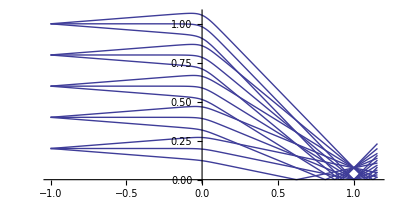

```mathematica
ParametricPlot[Table[{z[i][t]/targetfocus,r[i][t]/r0[[numrays]]}/.Flatten[sys],{i,numrays}],{t,0,tmax},AspectRatio->1/2]
```

```mathematica
(*Export["LoopLens.svg",%]*)
```

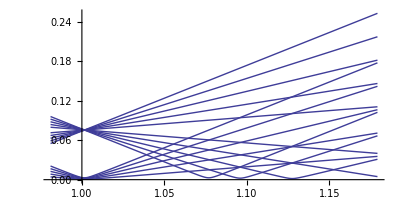

```mathematica
ParametricPlot[Table[{z[i][t]/targetfocus,r[i][t]/r0[[numrays]]}/.Flatten[sys],{i,numrays}],{t,1.5*10^-9,1.65*10^-9},AspectRatio->1/2]
```

```mathematica
(*Export["LoopZoom.svg",%]*)
```

Plot of x as t

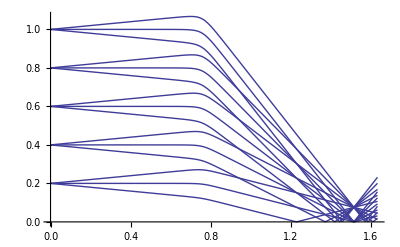

```mathematica
Plot[Table[r[i][t]/r0[[numrays]],{i,numrays}]/.sys,{t,0,tmax}]
```

```mathematica
D[z[1][t]/.Flatten[sys],t]/.t->99tmax/100
```

8.38628×10^7

```mathematica
t1=NMinimize[{Sum[Exp[-(r0[[i]]/w)^2]*r0[[i]]*(r[i][t]/.Flatten[sys]),{i,numrays}]/Sum[Exp[-(r0[[i]]/w)^2]*r0[[i]],{i,numrays}],0≤t≤tmax},t]
```

{0.0000101678,{t→1.51579×10^-9}}

```mathematica
tlc=t/.t1[[2]]
```

1.51579×10^-9

```mathematica
zlc=(z[1][t]/.Flatten[sys]/.{t->tlc})*10^6
```

63618.3

```mathematica
zlc/(targetfocus*10^6)
```

1.00186

```mathematica
t2=NMinimize[{Abs[r[3][t]]/.Flatten[sys],0≤t≤tmax},t]
```

{1.15034×10^-7,{t→1.51598×10^-9}}

```mathematica
tf=t/.t2[[2]]
```

1.51598×10^-9

```mathematica
zf=(z[1][t]/.Flatten[sys]/.{t->tf})*10^6
```

63634.3

```mathematica
zf/(targetfocus*10^6)
```

1.00212

```mathematica
Cs=zf-zlc
```

16.0641

```mathematica
data={{100,11},{200,51},{500,336},{750,741},{1000,1297}}
```

{{100,11},{200,51},{500,336},{750,741},{1000,1297}}

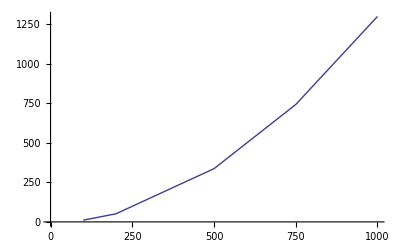

```mathematica
ListLinePlot[data]
```

```mathematica
Fit[data,{1,x,x^2},x]
```

-11.2987+0.0795334 x+0.00122936 x^2

```mathematica
pp3d=Join[Table[{(r[i][t]*Cos[ϕ[i][t]])/r0[[numrays]],(r[i][t]*Sin[ϕ[i][t]])/r0[[numrays]],(z[i][t])/targetfocus},{i,numrays}],Table[{(r[i][t]*Sin[ϕ[i][t]])/r0[[numrays]],(-r[i][t]*Cos[ϕ[i][t]])/r0[[numrays]],(z[i][t])/targetfocus},{i,numrays}],{1.2*Cos[2*π*t/tmax],1.2*Sin[2*π*t/tmax],0}];
```

```mathematica
(*ParametricPlot3D[pp3d/.Flatten[sys],{t,0,tmax},Boxed->False(*,ViewPoint->{2,-2,0.5}*)]*)
```

-Graphics3D-

```mathematica
(*Export["lens3d.svg",%]*)
```

```mathematica
numpoints=200
splittime=1.35*10^-9
dt1=splittime/numpoints;
dt2=(tmax-splittime)/numpoints;
multiplier=((r[numrays][t]/.sys/.t->0)/(r[numrays-2][t]/.sys/.t->splittime))[[1]]
```

200

1.35×10^-9

3.39341

```mathematica
(*outputtable=Table[Join[
Flatten[Table[{z[i][t],r[i][t]}/.Flatten[sys],{i,numrays}]/.t->(i*dt1)],Flatten[Table[{z[i][t],multiplier*r[i][t]}/.Flatten[sys],{i,numrays}]/.t->(i*dt2+splittime)]]
,{i,0,numpoints}];*)
```

```mathematica
outputtable=Table[
Flatten[{z[1][t]/.Flatten[sys],Table[r[i][t]/.Flatten[sys],{i,numrays}]}/.t->(j*tmax/numpoints)]
,{j,0,numpoints}];
```

```mathematica
Export[StringJoin[NotebookDirectory[],"mag_lens_kinematic.csv"],outputtable]
```

/home/joel/Documents/Thesis/inc/extension/external_forces/mag_lens_kinematic.csv